# \[MathematicaIcon]Curva de Rotação ESO 116-G12\[MathematicaIcon]

## Utilitários

Massa Solar → Grama 


Kpc → Cm 

Densidades

## Tabelas

```mathematica
data= Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\Fitting\\116.dat"];
Subscript[RC, total]=Table[{data[[i,1]],data[[i,3]]},{i,1,15}];
Subscript[RC, gas]=Table[{data[[i,1]],data[[i,4]]},{i,1,15}];
Erro = Table[data[[i,5]],{i,1,15}];
TableForm[data,TableHeadings->{{""},{"Raio","","Vtotal","Vgas","Erro"}}]
```

| Raio |  | Vtotal | Vgas | Erro
 | 0.295522 | 7.58904 | 20.94 | -0.234178 | 3.4
 | 0.985821 | 7.79329 | 39.95 | -1.95065 | 3.29
 | 1.62537 | 8.47973 | 51.54 | -1.68024 | 2.96
 | 2.18881 | 9.15955 | 67.92 | 5.43454 | 3.45
 | 3.17687 | 9.76846 | 80.22 | 13.5993 | 2.93
 | 3.76791 | 9.48569 | 83.33 | 18.0705 | 3.08
 | 4.35896 | 8.74732 | 91.38 | 21.8567 | 2.83
 | 4.8903 | 7.95629 | 101.65 | 24.2219 | 5.4
 | 6.19403 | 6.20847 | 104.77 | 27.7912 | 4.21
 | 7.16418 | 5.25717 | 108.62 | 29.5757 | 2.1
 | 8.0597 | 4.68539 | 108.48 | 30.9882 | 2.1
 | 8.95522 | 4.27244 | 108.73 | 33.3072 | 2.1
 | 9.85075 | 3.43065 | 110.24 | 36.6602 | 2.1
 | 10.7463 | 1.87414 | 110.63 | 38.4926 | 2.33
 | 11.6418 | 0.66706 | 111.52 | 36.585 | 4.74

## Valores de Parâmetros

```mathematica
Subscript[Tabela, Vdisk]=TableForm[Subscript[P, stars]= {{10^0.2,10^9},{10^0.3,10^9.8},{10^0.4,10^10.4},{10^0.7,10^11}},TableHeadings->{{"1","2","3","4"},{"R_d","M_d"}}];
Subscript[Tabela, Vdm]=TableForm[Subscript[P, dm]={{10^-0.5,4.1*10^8},{1,1.05*10^8},{10^0.5,2.5*10^7},{10^0.8,9.7*10^6},{10,5.7*10^6},{10^1.2,3.9*10^6},{10^1.4,2.3*10^6},{10^1.6,1.4*10^6}},TableHeadings->{{"Dwarf Spiral","","","Spiral Galaxy"},{"R_0","P_0"}}];
G:=4.302/10^6;

{Subscript[Tabela, Vdisk],Subscript[Tabela, Vdm]}
```

{ | R_d | M_d
1 | 1.58489 | 1000000000
2 | 1.99526 | 6.30957×10^9
3 | 2.51189 | 2.51189×10^10
4 | 5.01187 | 100000000000, | R_0 | P_0
Dwarf Spiral | 0.316228 | 4.1×10^8
 | 1 | 1.05×10^8
 | 3.16228 | 2.5×10^7
Spiral Galaxy | 6.30957 | 9.7×10^6
 | 10 | 5.7×10^6
 | 15.8489 | 3.9×10^6
 | 25.1189 | 2.3×10^6
 | 39.8107 | 1.4×10^6}

## Conversor de Unidades

```mathematica
ConversorKpc =DynamicModule[{a=0,b=0},Deploy[Style[Panel[Grid[Transpose[{{Style["Valor em Cm",Red],Style["Valor em Kpc",Blue],"Valor em Kpc", "Valor em Cm"},{InputField[Dynamic[a],Number],InputField[Dynamic[b],Number],InputField[Dynamic[N[a/(3.08*10^21)]]],InputField[Dynamic[b*(3.08*10^21)],Enabled->False]}}]],Alignment->Right,ImageMargins->10],DefaultOptions->{InputField->{FieldSize{{5,30},{1,Infinity}}}}]]];

ConversorMsol =DynamicModule[{a=0,b=0},Deploy[Style[Panel[Grid[Transpose[{{Style["Massa Solar",Red],Style["Grama",Blue],"Valor em Grama", "Valor em Msol"},{InputField[Dynamic[a],Number],InputField[Dynamic[b],Number],InputField[Dynamic[N[a*(1.99*10^33)]]],InputField[Dynamic[N[b/(1.99*10^33)]],Enabled->False]}}]],Alignment->Right,ImageMargins->10],DefaultOptions->{InputField->{FieldSize{{5,30},{1,Infinity}}}}]]];
ConversorDensidade =DynamicModule[{a=0,b=0},Deploy[Style[Panel[Grid[Transpose[{{Style["Densidade em Msol/Kpc^3",Red],Style["Densidade em g/cm^3",Blue],"g/Cm^3", "Msol/Kpc^3"},{InputField[Dynamic[a]],InputField[Dynamic[b]],InputField[Dynamic[N[a*(6.47*10^-32)]]],InputField[Dynamic[N[b*(1.5*10^31)]],Enabled->False]}}]],Alignment->Right,ImageMargins->10],DefaultOptions->{InputField->{FieldSize{{5,30},{1,Infinity}}}}]]];
```

## Equações

#### Velocidade das Estrelas no Disco

```mathematica
Subscript[V^2, disk][r_]=1/(2 Subscript[R, d])(G Subscript[M, d] (r/Subscript[R, d])^2) (BesselI[0,r/(2 Subscript[R, d])] BesselK[0,r/(2 Subscript[R, d])]-BesselI[1,r/(2 Subscript[R, d])] BesselK[1,r/(2 Subscript[R, d])]);
```

#### Velocidade Matéria Escura

```mathematica
Subscript[V^2, Dm][r_]=(6.4 G (Subscript[P, o] Subscript[R, o]^3) (1/2 Log[(r/Subscript[R, o])^2+1]+Log[r/Subscript[R, o]+1]-ArcTan[r/Subscript[R, o]]))/r;
```

#### Velocidade Total

```mathematica
Subscript[V, t][r_]=Sqrt[Subscript[V^2, disk][r]+Subscript[V^2, Dm][r]+Igas[r]^2];
```

## Interpolação do Gás

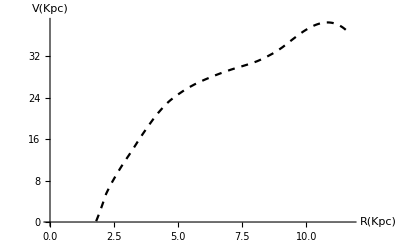

```mathematica
Igas=Interpolation[Subscript[RC, gas]];
Subscript[V^2, gas]=(Igas^2)[r];
Gas= Plot[Igas[x],{x,1.8,11.7},AxesOrigin->{x=0,x=0},PlotStyle->{Black,Dashed},AxesLabel->{"R(Kpc)","V(Kpc)"}]
```

## Gráfico Velocidade das estrelas no disco

```mathematica
Subscript[V, d1]=Plot[√(Subscript[V^2, disk][r])/.{Subscript[R, d]->1.58,Subscript[M, d]->10^9},{r,0,20}] ;
Subscript[V, d2]=Plot[√(Subscript[V^2, disk][r])/.{Subscript[R, d]->1.99,Subscript[M, d]->6.3*10^9},{r,0,30}] ;
Subscript[V, d3]=Plot[√(Subscript[V^2, disk][r])/.{Subscript[R, d]->2.51,Subscript[M, d]->2.5*10^10},{r,0,40}] ;
Subscript[V, d4]=Plot[√(Subscript[V^2, disk][r])/.{Subscript[R, d]->5.01,Subscript[M, d]->10^11},{r,0,50}] ;
Subscript[V, d]=Show[Subscript[V, d1],Subscript[V, d2],Subscript[V, d3],Subscript[V, d4],Frame->True,PlotRange->All,AspectRatio->0.8,PlotLabel->"Estrelas no disco",AxesLabel->{"R(Kpc)","V(Km/s)"}];
```

## Gráfico Velocidade Matéria Escura

```mathematica
Subscript[V, dm1]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->0.32,Subscript[P, o]->4.1 10^8},{r,0,10},PlotRange->All];
Subscript[V, dm2]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->1,Subscript[P, o]->1.05 10^8},{r,0,12},PlotRange->All];
Subscript[V, dm3]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->3.16,Subscript[P, o]->2.5 10^7},{r,0,20},PlotRange->All];
Subscript[V, dm4]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->6.31,Subscript[P, o]->9.7 10^6},{r,0,45},PlotRange->All];
Subscript[V, dm5]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->10,Subscript[P, o]->5.7 10^6},{r,0,60},PlotRange->All];
Subscript[V, dm6]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->15.85,Subscript[P, o]->3.9 10^6},{r,0,70},PlotRange->All];
Subscript[V, dm7]= Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->25.12,Subscript[P, o]->2.3 10^6},{r,0,100},PlotRange->All];
Subscript[V, dm8]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->39.81,Subscript[P, o]->1.4 10^6},{r,0,125},PlotRange->All];
Show[Subscript[V, dm1],Subscript[V, dm2],Subscript[V, dm3]];
Subscript[V, dm]=Show[Subscript[V, dm4],Subscript[V, dm5],Subscript[V, dm6],Subscript[V, dm7],Subscript[V, dm8], Frame->True,PlotRange->All,AspectRatio->0.75,PlotLabel->"Modelo de Burket para o Halo de Matéria Escura"];
```

## Modelo de Burket ESO 116-G12

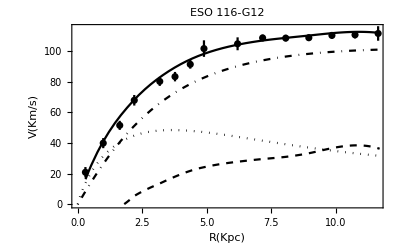

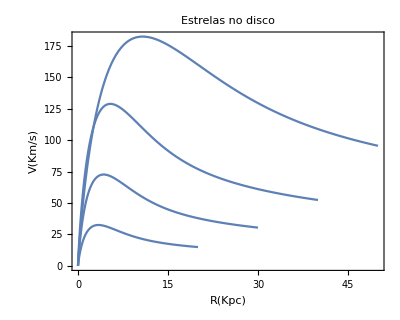
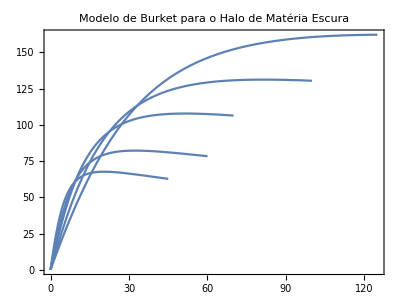

```mathematica
Needs["ErrorBarPlots`"];
Subscript[CR, tot]=ErrorListPlot[{Table[{Subscript[RC, total]⟦i⟧,ErrorBar[Erro⟦i⟧]},{i,15}]},PlotStyle->Black,MeshStyle->PointSize[Large]];
Subscript[RC, stars]=Plot[√(Subscript[V^2, disk][r])/.{Subscript[M, d]->2.4 10^9,Subscript[R, d]->1.7},{r,0,11.7},PlotStyle->{Black,Dotted}];
Subscript[RC, halo]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->4.3,Subscript[P, o]->4.7 10^7},{r,0,11.7},PlotStyle->{Black,DotDashed}];
Subscript[RC, vtot]=Plot[Subscript[V, t][r]/.{Subscript[M, d]->2.4 10^9,Subscript[R, d]->1.7,Subscript[R, o]->4.3,Subscript[P, o]->4.7 10^7},{r,0.3,11.6},PlotStyle->Black,PlotRange->Automatic];
Show[Subscript[CR, tot],Subscript[RC, stars],Subscript[RC, halo],Subscript[RC, vtot],Gas,Frame->True,PlotRange->{{0,11.6},{0,115}},PlotLabel->"ESO 116-G12",FrameLabel->{"R(Kpc)","V(Km/s)"}]
Table[{Subscript[V, d],Subscript[V, dm]}]
```

## Ajuste Linear

```mathematica
Clear[x]
```

FittedModel[0.193333+2.1303 x]

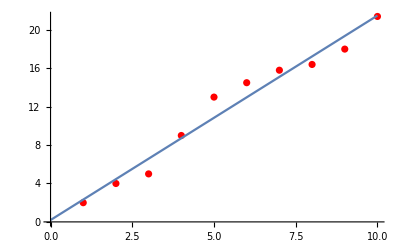

FittedModel[0.193333+2.1303 x]

```mathematica
f[x_,c_,d_]:=c+d*x;
Subscript[data, a] = Table[{2,4,5,9,13,14.5,15.8,16.4,18,21.4}];
LMF =LinearModelFit[Subscript[data, a],x,x]
   Ajuste =Show[ListPlot[Subscript[data, a],PlotStyle->Red],Plot[LMF[x],{x,0,10}]]
Subscript[Ajuste, 1]=NonlinearModelFit[Subscript[data, a],f[x,c,d],{{c,0.5},{d,3}},x]
Clear[f];
```

FittedModel[1.93982+3.15317 x+2.40117 x^2]

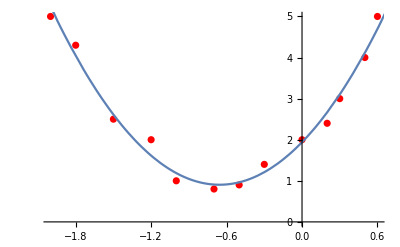

```mathematica
f[x_,a_,b_,c_]:=a+b*x+c*x^2;
datab = Table[{{-2,5},{-1.8,4.3},{-1.5,2.5},{-1.2,2},{-1,1},{-0.7,0.8},{-0.5,0.9},{-0.3,1.4},{0,2},{0.2,2.4},{0.3,3},{0.5,4},{0.6,5}}];
Subscript[Fit, 1] =NonlinearModelFit[datab,f[x,b,c,a],{{a,2},{b,4},{c,2}},x]
Show[ListPlot[datab,PlotStyle->Red],Plot[Subscript[Fit, 1][r],{r,-5,5}]]
Clear[f];
```

## Ajuste Não Linear

FittedModel[√(905.618 r^2 (BesselI[0,0.294118 r] BesselK[0,0.294118 r]-BesselI[1,0.294118 r] BesselK[1,0.294118 r])+(129439. (-ArcTan[0.214452 r]+Log[1+«20» r]+1/2 Log[1+0.0459897 r^2]))/r)]

| Estimate | Standard Error | t-Statistic | P-Value
M | 2.06848 | 0.687315 | 3.00951 | 0.0108728
P | 4.63667 | 1.15787 | 4.00447 | 0.00174759
R | 4.66305 | 0.626713 | 7.44048 | 7.83508×10^-6

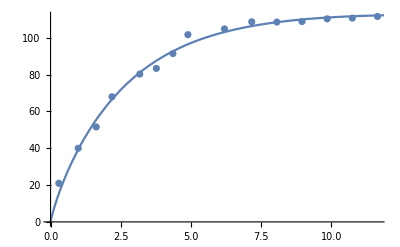

```mathematica
Clear[f]
VDisk[r_,M_]:=1/(2 Subscript[R, d])(G (M*10^9) (r/Subscript[R, d])^2) (BesselI[0,r/(2 Subscript[R, d])] BesselK[0,r/(2 Subscript[R, d])]-BesselI[1,r/(2 Subscript[R, d])] BesselK[1,r/(2 Subscript[R, d])]);
VDark[r_,R_,P_]:=(6.4 G ((P *10^7) R^3) (1/2 Log[(r/R)^2+1]+Log[r/R+1]-ArcTan[r/R]))/r;
h[r_,R_,P_,M_]:= Sqrt[VDisk[r,M]+VDark[r,R,P]];
Subscript[R, d]:=1.7;

Fit2=NonlinearModelFit[Subscript[RC, total],h[r,R,P,M],{{M,0.1,10},{P,0.1,10},{R,1,10}},r]
Fit2["ParameterTable"]
Show[ListPlot[Subscript[RC, total]],Plot[Fit2[r],{r,0,100},AxesOrigin->{0,0}]]
```

FittedModel[√(952.28 r^2 (BesselI[0,0.294118 r] BesselK[0,0.294118 r]-BesselI[1,0.294118 r] BesselK[1,0.294118 r])+(106866. (-ArcTan[0.226155 r]+Log[«1»]+1/2 Log[1+0.0511459 «1»]))/r+(InterpolatingFunction[{{0.295522, 11.6418}}, <>][r])^2)]

| Estimate | Standard Error | t-Statistic | P-Value
M | 2.17506 | 0.745273 | 2.91847 | 0.0128768
P | 4.48958 | 1.33741 | 3.35691 | 0.00570668
R | 4.42175 | 0.688177 | 6.42532 | 0.0000327752

InterpolatingFunction::dmval: Input value {0.00204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

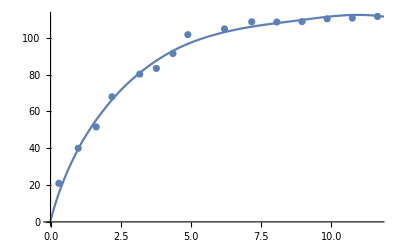

```mathematica
j[r_,R_,P_,M_]:=Sqrt[VDisk[r,M]+VDark[r,R,P]+Igas[r]^2]
Fit3=NonlinearModelFit[Subscript[RC, total],j[r,R,P,M],{{M,0.1,10},{P,0.1,10},{R,1,10}},r]
Fit3["ParameterTable"]
Show[ListPlot[Subscript[RC, total]],Plot[Fit3[r],{r,0,100},AxesOrigin->{0,0}]]
```

## Gráficos do Ajuste

InterpolatingFunction::dmval: Input value {0.000236971} lies outside the range of data in the interpolating function. Extrapolation will be used.

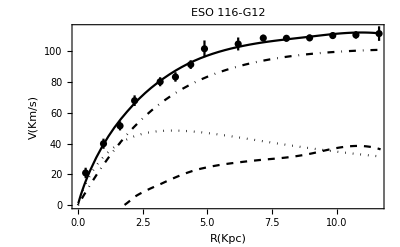

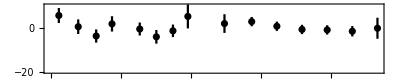

```mathematica
FINAL=Plot[Subscript[V, t][r]/.{Subscript[M, d]->2.17 *10^9,Subscript[R, d]->1.7,Subscript[R, o]->4.42,Subscript[P, o]->4.48 10^7},{r,0,11.6},PlotStyle->Black,PlotRange->Automatic];
Show[Subscript[CR, tot],Subscript[RC, stars],Subscript[RC, halo],FINAL,Gas,Frame->True,PlotRange->{{0,11.6},{0,115}},PlotLabel->"ESO 116-G12",FrameLabel->{"R(Kpc)","V(Km/s)"}]
FITERRO = Table [{data[[i,1]],Fit3["FitResiduals"][[i]]},{i,15}];
ErrorListPlot[{Table[{FITERRO[[i]], ErrorBar[Erro[[i]]]}, {i, 15}]}, PlotStyle -> Black, MeshStyle -> PointSize[Large], PlotRange->{-20,10},Frame->True,AspectRatio->0.2]
```

## Tabelas 2

```mathematica
data2 = Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\data_new\\287.dat"];
data3 = Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\data_new\\1090.dat"];
data4 = Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\data_new\\7339.dat"];
RC287=Table[{data2[[i,1]],data2[[i,3]]},{i,1,26}];
RCgas2=Table[{data2[[i,1]],data2[[i,4]]},{i,1,26}];
Erro2 = Table[data2[[i,5]],{i,1,26}]; 

RC1090=Table[{data3[[i,1]],data3[[i,3]]},{i,1,24}];
RCgas3=Table[{data3[[i,1]],data2[[i,4]]},{i,1,24}];
Erro3 = Table[data3[[i,5]],{i,1,24}]; 

RC7339=Table[{data4[[i,1]],data4[[i,3]]},{i,1,15}];
RCgas4=Table[{data4[[i,1]],data4[[i,4]]},{i,1,15}];
Erro4 = Table[data4[[i,5]],{i,1,15}]; 

TableForm[data2,TableHeadings->{{"ESO 287-G13"},{"Raio","","Vtotal","Vgas","Erro"}} ]
TableForm[data3,TableHeadings->{{"NGC 1090"},{"Raio","","Vtotal","Vgas","Erro"}}]
TableForm[data4,TableHeadings->{{"NGC 7339"},{"Raio","","Vtotal","Vgas","Erro"}}]
```

| Raio |  | Vtotal | Vgas | Erro
ESO 287-G13 | 0.27931 | 9.14305 | 15.76 | 1.07424 | 3.87
 | 0.837931 | 8.9123 | 42.49 | 2.46665 | 4.93
 | 1.39655 | 8.75228 | 70.03 | 3.27774 | 10.44
 | 1.95517 | 8.66275 | 105.83 | 3.68792 | 4.
 | 2.51379 | 8.64403 | 118.54 | 3.84641 | 4.
 | 3.07241 | 8.69604 | 126.9 | 3.88202 | 3.08
 | 3.63103 | 8.81861 | 140.32 | 4.1325 | 4.
 | 4.18966 | 9.00001 | 144.27 | 5.44853 | 4.02
 | 4.74828 | 9.09676 | 155.65 | 7.01228 | 5.36
 | 5.3069 | 9.19495 | 149.54 | 8.38873 | 5.41
 | 5.86552 | 9.29563 | 150.65 | 9.76333 | 7.06
 | 6.42414 | 9.40034 | 155.02 | 11.1443 | 4.66
 | 6.98276 | 9.51116 | 166.94 | 12.5646 | 6.
 | 7.54138 | 9.62647 | 167.37 | 14.0251 | 2.63
 | 8.1 | 9.74586 | 163.17 | 15.4947 | 3.32
 | 8.65862 | 9.89069 | 164.38 | 16.9319 | 2.43
 | 9.21724 | 10.0609 | 160.2 | 18.5489 | 5.7
 | 9.77586 | 10.2493 | 164.47 | 20.3382 | 3.79
 | 10.3345 | 10.4562 | 172.81 | 22.3449 | 8.51
 | 10.8931 | 10.6663 | 165.95 | 24.5708 | 2.
 | 15.3621 | 11.3032 | 163.72 | 52.6146 | 10.79
 | 15.9207 | 10.7869 | 173.94 | 56.4422 | 2.
 | 18.6207 | 6.81669 | 176.44 | 67.7037 | 2.8
 | 20.6897 | 4.2309 | 182.08 | 68.486 | 2.31
 | 22.7586 | 2.37977 | 184.16 | 66.5516 | 2.07
 | 24.8276 | 1.2192 | 183.3 | 62.8426 | 2.05

| Raio |  | Vtotal | Vgas | Erro
NGC 1090 | 0.347368 | 3.4723 | 20.88 | -0.813067 | 9.81
 | 1.04211 | 3.50686 | 61.73 | -2.48381 | 8.19
 | 1.56316 | 3.57333 | 81.26 | -3.69901 | 4.32
 | 3.62105 | 4.04191 | 124.02 | -7.34289 | 3.41
 | 4.98246 | 4.42132 | 156.15 | -9.31053 | 7.02
 | 6.46667 | 5.10939 | 166.47 | -10.7933 | 6.34
 | 7.98947 | 6.01784 | 165.26 | -5.73686 | 12.05
 | 8.91228 | 6.38245 | 173.99 | 9.56049 | 4.84
 | 10.1018 | 6.58873 | 164.38 | 17.7079 | 5.86
 | 10.9965 | 6.53136 | 175.97 | 22.4891 | 7.35
 | 13.3193 | 5.92514 | 174.02 | 31.6324 | 3.28
 | 14.7368 | 5.41066 | 167.69 | 35.2506 | 2.23
 | 15.9649 | 4.92757 | 166.39 | 37.8353 | 2.23
 | 17.193 | 4.49278 | 167.05 | 39.7589 | 4.59
 | 18.4211 | 4.058 | 166.57 | 41.3701 | 5.3
 | 19.6491 | 3.67152 | 165.26 | 42.479 | 3.48
 | 20.8772 | 3.33335 | 164.83 | 43.2492 | 3.12
 | 22.1053 | 3.09181 | 164.98 | 43.7767 | 2.39
 | 23.3333 | 2.94688 | 164.6 | 44.6902 | 2.23
 | 24.5614 | 2.75364 | 162.77 | 46.2975 | 2.23
 | 25.7895 | 2.51209 | 162.08 | 47.9662 | 2.23
 | 27.0175 | 2.22224 | 162.23 | 49.6384 | 2.23
 | 28.2456 | 1.83576 | 161.54 | 51.024 | 2.23
 | 29.4737 | 1.34984 | 160.18 | 52.0913 | 2.23

| Raio |  | Vtotal | Vgas | Erro
NGC 7339 | 0.17069 | 3.53707 | 25.81 | -1.34586 | 5.54
 | 0.512069 | 4.03218 | 63.14 | -3.60897 | 4.02
 | 0.853448 | 4.80899 | 88.79 | -5.43247 | 3.98
 | 1.19483 | 5.86751 | 118.89 | -6.37706 | 9.48
 | 1.53621 | 6.75684 | 116.06 | -5.77815 | 2.26
 | 1.87759 | 7.50929 | 127.75 | -1.61714 | 2.62
 | 2.21897 | 7.72679 | 135.88 | 6.71423 | 2.8
 | 2.56034 | 7.79803 | 140. | 8.8814 | 3.16
 | 2.90172 | 8.19568 | 144.13 | 11.4071 | 2.33
 | 3.2431 | 8.44312 | 153.73 | 15.0866 | 2.92
 | 3.58448 | 8.38166 | 150.78 | 18.7424 | 3.08
 | 3.92586 | 7.73976 | 160.02 | 22.3997 | 3.01
 | 4.26724 | 6.62754 | 161.4 | 24.5162 | 2.14
 | 4.66724 | 5.80733 | 169.09 | 26.0432 | 10.14
 | 5.43103 | 4.14981 | 159.5 | 29.4017 | 2.04

## Interpolação Gás 2

InterpolatingFunction[{{0.27931, 24.8276}}, <>]

InterpolatingFunction::dmval: Input value {0.200503} lies outside the range of data in the interpolating function. Extrapolation will be used.

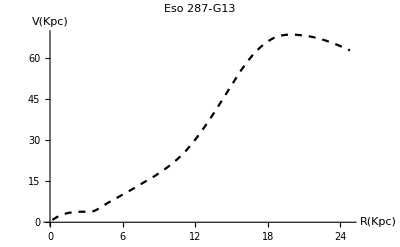

InterpolatingFunction::dmval: Input value {0.300594} lies outside the range of data in the interpolating function. Extrapolation will be used.

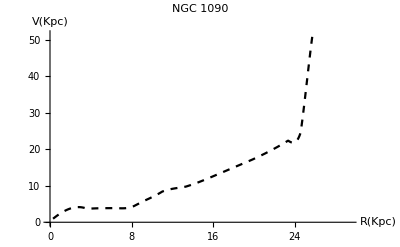

InterpolatingFunction::dmval: Input value {0.100108} lies outside the range of data in the interpolating function. Extrapolation will be used.

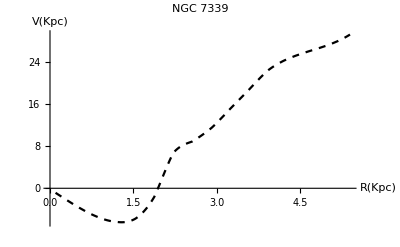

```mathematica
AAAA= Interpolation[RCgas2]
Igas3 = Interpolation[RCgas3];
Igas4 = Interpolation[RCgas4];
Gas287 = Plot[Igas2[r],{r,0.2,24.8},AxesOrigin->{x=0,x=0},PlotStyle->{Black,Dashed},AxesLabel->{"R(Kpc)","V(Kpc)"} , PlotLabel->"Eso 287-G13"]
Gas1090 = Plot[Igas3[r], {r,0.3, 29.4},AxesOrigin->{x=0,x=0},PlotStyle->{Black,Dashed},AxesLabel->{"R(Kpc)","V(Kpc)"}, PlotLabel->"NGC 1090"]
Gas7339 = Plot[Igas4[r],{r,0.1,5.4},AxesOrigin->{x=0,x=0},PlotStyle->{Black,Dashed},AxesLabel->{"R(Kpc)","V(Kpc)"},PlotLabel->"NGC 7339"]
```

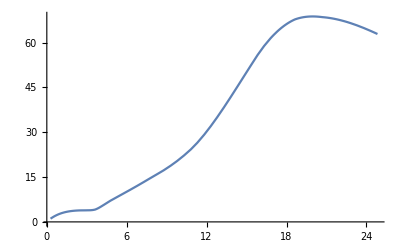

```mathematica
Plot[Igas2[x],{x,0.27931,24.8276}]
```

## Ajuste 2

```mathematica
V1[r_,M_]:=1/(2 Rd)(G (M*10^9) (r/Rd)^2) (BesselI[0,r/(2 Rd)] BesselK[0,r/(2 Rd)]-BesselI[1,r/(2 Rd)] BesselK[1,r/(2 Rd)]);
V2[r_,R_,P_]:=(6.4 G ((P *10^7) R^3) (1/2 Log[(r/R)^2+1]+Log[r/R+1]-ArcTan[r/R]))/r;
```

```mathematica
Rd:=3.3;
k[r_,R_,P_,M_]:=√(V1[r,M]+V2[r,R,P]+AAAA[r]*AAAA[r]);
Fit287=NonlinearModelFit[RC287,k[r,R,P,M],{{M,0.1,10},{P,0.1,10},{R,1,25}},r];
Fit287["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
M | 64.8387 | 9.69317 | 6.68911 | 7.99319×10^-7
P | -77.1957 | 59.9685 | -1.28727 | 0.210804
R | 0.627151 | 0.492653 | 1.27301 | 0.215733

InterpolatingFunction::dmval: Input value {0.00204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

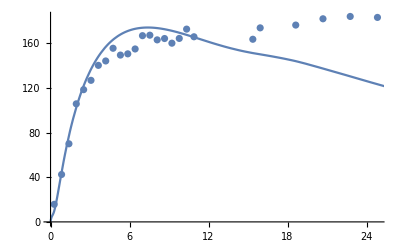

```mathematica
Show[ListPlot[RC287],Plot[Fit287[r],{r,0,100},AxesOrigin->{0,0}]]
```

```mathematica
Fit287["BestFit"]
```

√(3880.9 r^2 (BesselI[0,0.151515 r] BesselK[0,0.151515 r]-BesselI[1,0.151515 r] BesselK[1,0.151515 r])-(5242.75 (-ArcTan[1.59451 r]+Log[1+1.59451 r]+1/2 Log[1+2.54247 r^2]))/r+(InterpolatingFunction[{{0.27931, 24.8276}}, <>][r])^2)

```mathematica
l[r_,R_,P_,M_]:=√(VDisk[r,M]+VDark[r,R,P]+Igas3[r]^2);
m[r_,R_,P_,M_]:=√(VDisk[r,M]+VDark[r,R,P]+Igas4[r]^2);
Fit1090=NonlinearModelFit[RC1090,l[r,R,P,M],{{M,0.1,10},{P,0.1,10},{R,1,10}},r];
Fit7339=NonlinearModelFit[RC7339,m[r,R,P,M],{{M,0.1,10},{P,0.1,10},{R,1,10}},r];
```

| Estimate | Standard Error | t-Statistic | P-Value
M | 64.8387 | 9.69317 | 6.68911 | 7.9932×10^-7
P | -77.1957 | 59.9685 | -1.28727 | 0.210804
R | 0.627151 | 0.492653 | 1.27301 | 0.215733

Clear::ssym: R_d is not a symbol or a string.

```mathematica
Fit287["ParameterTable"]
Fit1090["ParameterTable"]
Fit7339["ParameterTable"]
```

InterpolatingFunction::dmval: Input value {0.27931} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15.3621} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15.9207} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value 2.06763×10^6-108.663 ⅈ is not a real number at {M,P,R} = {42.3748,-315.952,0.661489}.

NonlinearModelFit[{{0.27931,15.76},{0.837931,42.49},{1.39655,70.03},{1.95517,105.83},{2.51379,118.54},{3.07241,126.9},{3.63103,140.32},{4.18966,144.27},{4.74828,155.65},{5.3069,149.54},{5.86552,150.65},{6.42414,155.02},{6.98276,166.94},{7.54138,167.37},{8.1,163.17},{8.65862,164.38},{9.21724,160.2},{9.77586,164.47},{10.3345,172.81},{10.8931,165.95},{15.3621,163.72},{15.9207,173.94},{18.6207,176.44},{20.6897,182.08},{22.7586,184.16},{24.8276,183.3}},√(437.818 M r^2 (BesselI[0,0.294118 r] BesselK[0,0.294118 r]-BesselI[1,0.294118 r] BesselK[1,0.294118 r])+(275.328 P R^3 (-ArcTan[r/R]+1/2 Log[1+r^2/R^2]+Log[1+r/R]))/r+(InterpolatingFunction[{{0.295522, 11.6418}}, <>][r])^2),{{M,0.1,10},{P,0.1,10},{R,1,10}},r][ParameterTable]

InterpolatingFunction::dmval: Input value {13.3193} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {14.7368} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15.9649} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value 2.15157×10^7-3574.64 ⅈ is not a real number at {M,P,R} = {106.355,-508.666,0.972667}.

NonlinearModelFit[{{0.347368,20.88},{1.04211,61.73},{1.56316,81.26},{3.62105,124.02},{4.98246,156.15},{6.46667,166.47},{7.98947,165.26},{8.91228,173.99},{10.1018,164.38},{10.9965,175.97},{13.3193,174.02},{14.7368,167.69},{15.9649,166.39},{17.193,167.05},{18.4211,166.57},{19.6491,165.26},{20.8772,164.83},{22.1053,164.98},{23.3333,164.6},{24.5614,162.77},{25.7895,162.08},{27.0175,162.23},{28.2456,161.54},{29.4737,160.18}},√(437.818 M r^2 (BesselI[0,0.294118 r] BesselK[0,0.294118 r]-BesselI[1,0.294118 r] BesselK[1,0.294118 r])+(275.328 P R^3 (-ArcTan[r/R]+1/2 Log[1+r^2/R^2]+Log[1+r/R]))/r+(InterpolatingFunction[{{0.295522, 11.6418}}, <>][r])^2),{{M,0.1,10},{P,0.1,10},{R,1,10}},r][ParameterTable]

InterpolatingFunction::dmval: Input value {0.17069} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
M | 28.2664 | 12.5967 | 2.24395 | 0.0444797
P | -48.6005 | 44.9981 | -1.08006 | 0.301347
R | 0.785744 | 1.0758 | 0.730378 | 0.479176